```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pedro/seagate_4tb/Dropbox/Dropbox/beta-Planck/paper.draft/draft_v2/plots/plot_codes/final_hist_obs

```mathematica
ResourceFunction["MaTeXInstall"][]
```

Paclet[MaTeX,1.7.7,<>]

```mathematica
<<MaTeX`
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

```mathematica
betafid=0.00123357;
```

```mathematica
c=299792.458;
```

```mathematica
betafickms =betafid*c;
```

## Importing and reorganizing data

```mathematica
nilcresults=Import["data/nilc_obs_TTEE_ab_dopp_abdopp_CorrUnbiasedVEC_lmin_200_lmax_1800.dat"];
smicaresults=Import["data/smica_obs_TTEE_ab_dopp_abdopp_CorrUnbiasedVEC_lmin_200_lmax_1800.dat"];
nilcresultswDD=Import["data/nilc_obs_TTEE_w_DD_ab_dopp_abdopp_CorrUnbiasedVEC_lmin_200_lmax_1800.dat"];
smicaresultswDD=Import["data/smica_obs_TTEE_w_DD_ab_dopp_abdopp_CorrUnbiasedVEC_lmin_200_lmax_1800.dat"];
```

```mathematica
nilcSIMS=Import["data/nilcTTEE_with_absbias.hdf",{"Datasets","Dataset1"}]*c;
smicaSIMS=Import["data/smicaTTEE_with_absbias.hdf",{"Datasets","Dataset1"}]*c;
nilcSIMSwDD=Import["data/nilcTTEE_w_DD_with_absbias.hdf",{"Datasets","Dataset1"}]*c;
smicaSIMSwDD=Import["data/smicaTTEE_w_DD_with_absbias.hdf",{"Datasets","Dataset1"}]*c;
```

```mathematica
fiducialVECS=Import["data/xyz_fiducial_48_directions_vecs.dat"]*c;
dipole=Import["data/dipole_xyz_fiducial_vec.dat"][[All,1]]*c;
```

```mathematica
smicaTTEEabDiff=Flatten[Table[smicaSIMS[[1,dir,sim]]-fiducialVECS[[dir]],{dir,1,48},{sim,1,64}],1];
smicaTTEEdoppDiff=Flatten[Table[smicaSIMS[[2,dir,sim]]-fiducialVECS[[dir]],{dir,1,48},{sim,1,64}],1];
smicaTTEEpvDiff=Flatten[Table[smicaSIMS[[3,dir,sim]]-fiducialVECS[[dir]],{dir,1,48},{sim,1,64}],1];
nilcTTEEabDiff=Flatten[Table[nilcSIMS[[1,dir,sim]]-fiducialVECS[[dir]],{dir,1,48},{sim,1,64}],1];
nilcTTEEdoppDiff=Flatten[Table[nilcSIMS[[2,dir,sim]]-fiducialVECS[[dir]],{dir,1,48},{sim,1,64}],1];
nilcTTEEpvDiff=Flatten[Table[nilcSIMS[[3,dir,sim]]-fiducialVECS[[dir]],{dir,1,48},{sim,1,64}],1];
```

```mathematica
Dimensions[smicaTTEEpvDiff]
```

{3072,3}

```mathematica
StandardDeviation[smicaTTEEpvDiff[[All,3]]]
```

90.9485

```mathematica
smicaTTEEabDiffNULL=Flatten[Table[smicaSIMSwDD[[1,sim]],{sim,1,1024},{repeat,1,3}],1];
smicaTTEEdoppDiffNULL=Flatten[Table[smicaSIMSwDD[[2,sim]],{sim,1,1024},{repeat,1,3}],1];
smicaTTEEpvDiffNULL=Flatten[Table[smicaSIMSwDD[[3,sim]],{sim,1,1024},{repeat,1,3}],1];
nilcTTEEabDiffNULL=Flatten[Table[nilcSIMSwDD[[1,sim]],{sim,1,1024},{repeat,1,3}],1];
nilcTTEEdoppDiffNULL=Flatten[Table[nilcSIMSwDD[[2,sim]],{sim,1,1024},{repeat,1,3}],1];
nilcTTEEpvDiffNULL=Flatten[Table[nilcSIMSwDD[[3,sim]],{sim,1,1024},{repeat,1,3}],1];
```

```mathematica
vecsistbetaforhistsmica={{smicaTTEEabDiff[[All,1]],smicaTTEEdoppDiff[[All,1]],smicaTTEEpvDiff[[All,1]]},{smicaTTEEabDiff[[All,2]],smicaTTEEdoppDiff[[All,2]],smicaTTEEpvDiff[[All,2]]},{smicaTTEEabDiff[[All,3]],smicaTTEEdoppDiff[[All,3]],smicaTTEEpvDiff[[All,3]]}};
vecsistbetaforhistnilc={{nilcTTEEabDiff[[All,1]],nilcTTEEdoppDiff[[All,1]],nilcTTEEpvDiff[[All,1]]},{nilcTTEEabDiff[[All,2]],nilcTTEEdoppDiff[[All,2]],nilcTTEEpvDiff[[All,2]]},{nilcTTEEabDiff[[All,3]],nilcTTEEdoppDiff[[All,3]],nilcTTEEpvDiff[[All,3]]}};
```

```mathematica
vecsistbetaforhistsmicaNULL={{smicaTTEEabDiffNULL[[All,1]],smicaTTEEdoppDiffNULL[[All,1]],smicaTTEEpvDiffNULL[[All,1]]},{smicaTTEEabDiffNULL[[All,2]],smicaTTEEdoppDiffNULL[[All,2]],smicaTTEEpvDiffNULL[[All,2]]},{smicaTTEEabDiffNULL[[All,3]],smicaTTEEdoppDiffNULL[[All,3]],smicaTTEEpvDiffNULL[[All,3]]}};
vecsistbetaforhistnilcNULL={{nilcTTEEabDiffNULL[[All,1]],nilcTTEEdoppDiffNULL[[All,1]],nilcTTEEpvDiffNULL[[All,1]]},{nilcTTEEabDiffNULL[[All,2]],nilcTTEEdoppDiffNULL[[All,2]],nilcTTEEpvDiffNULL[[All,2]]},{nilcTTEEabDiffNULL[[All,3]],nilcTTEEdoppDiffNULL[[All,3]],nilcTTEEpvDiffNULL[[All,3]]}};
```

```mathematica
Total[(nilcresultswDD[[2]]*c/{StandardDeviation[nilcTTEEdoppDiffNULL[[All,1]]],StandardDeviation[nilcTTEEdoppDiffNULL[[All,2]]],StandardDeviation[nilcTTEEdoppDiffNULL[[All,3]]]})^2]
```

13.7859

```mathematica
Dimensions[vecsistbetaforhistnilc]
```

{3,3,3072}

```mathematica
ticks[min_,max_,stepsz_,majdivs_,baselength_,insideticks_?BooleanQ,labels_?BooleanQ,cutmin_,cutmax_]:=Table[{i,If[i<=cutmax,If[i>=cutmin,If[Mod[i-min,majdivs]==0∧labels,ToString[Round@i],""],""],""],If[insideticks,#,Reverse[#]]&[{If[Mod[i-min,majdivs]==0,2 baselength,baselength],0}]},{i,min,max,stepsz}]
ticks2[min_,max_,stepsz_,majdivs_,majdivslabel_,baselength_,insideticks_?BooleanQ,labels_?BooleanQ,cutmin_,cutmax_]:=Table[{i,If[i<=cutmax,If[i>=cutmin,If[Mod[i,majdivslabel]==0∧labels,ToString[Round@i],""],""],""],If[insideticks,#,Reverse[#]]&[{If[Mod[i-min,majdivs]==0,2 baselength,baselength],0}]},{i,min,max,stepsz}]
```

## Plots

```mathematica
plotrange=890;
frametickness=2;
trianglesize=34;
color1=Gray;alpha1=0.4;
color2=RGBColor[0.5,0.13,0.71,0.7];alpha2=0.4;
color3=Blue(*RGBColor[0, 0.61, 0];*)
color4=Red(*RGBColor[0.86, 0.52, 0];*)
color1t=RGBColor[0.5,0.5,0.5,0.7];
color2t=RGBColor[0.5,0.13,0.71,0.7]
labelfontsize=26;
ticksfontsize=22;
legend1=MaTeX["\\boldsymbol{\\beta}\\!=\\!\\boldsymbol{\Delta_1} ",Magnification->1.75]
legend2=MaTeX["\\boldsymbol{\\beta}\\!=\\!\\boldsymbol{0} ",Magnification->1.75]
legendx=MaTeX["c \\beta_x \\rm{(km/s)}",Magnification->2.5]
legendy=MaTeX["c \\beta_y \\rm{(km/s)}",Magnification->2.5]
legendz=MaTeX["c \\beta_z \\rm{(km/s)}",Magnification->2.5]
r1=r2=0.03;
```

RGBColor[0, 0, 1]

RGBColor[1, 0, 0]

RGBColor[0.5, 0.13, 0.71, 0.7]

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
selectrange[list_]:=Select[list,Abs[#]<899&]
```

```mathematica
Export["test.pdf",legend1]
```

test.pdf

```mathematica
triangleposcorrection=1.0144;
```

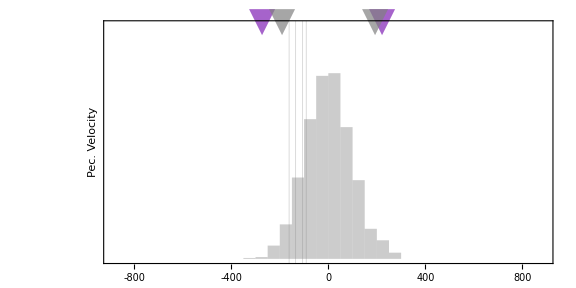

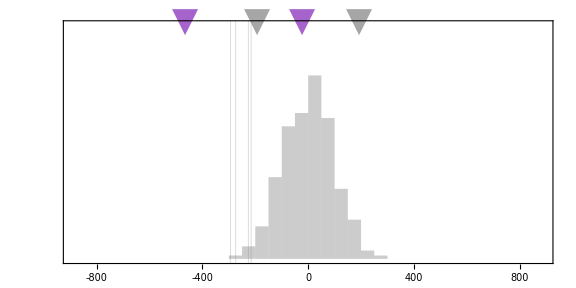

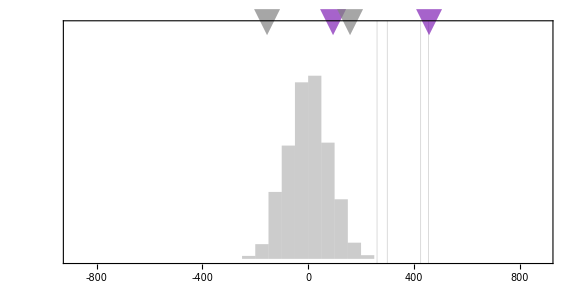

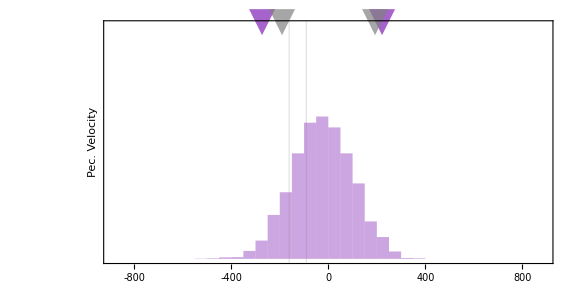

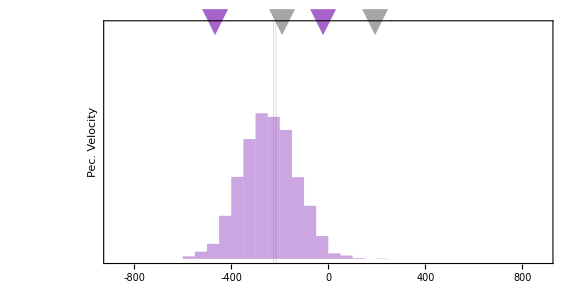

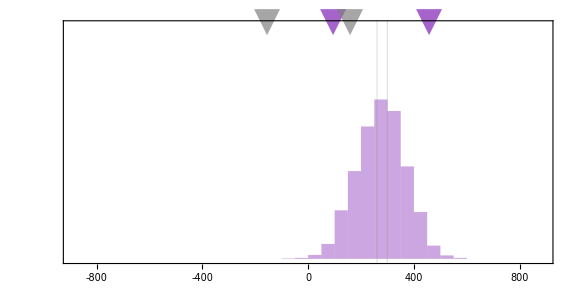

```mathematica
estim=3;
axis=1;
countmax=660*1.2;
pvxNULL=Histogram[vecsistbetaforhistsmicaNULL[[axis]][[estim]],10,ChartStyle->Directive[Opacity[alpha1,color1],EdgeForm[None]],Frame->True,FrameLabel->{legendx,Style["Pec. Velocity",labelfontsize]},GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{(nilcresultswDD[[estim]][[axis]]*c),{color3,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}},{smicaresultswDD[[estim]][[axis]]*c,{color4,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,True,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,True,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finalpvxNULL=Show[{pvxNULL,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
axis=2;
countmax=700*1.2;
pvyNULL=Histogram[vecsistbetaforhistsmicaNULL[[axis]][[estim]],10,ChartStyle->Directive[Opacity[alpha1,color1],EdgeForm[None]],Frame->True,GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{(nilcresultswDD[[estim]][[axis]]*c),{color3,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}},{smicaresultswDD[[estim]][[axis]]*c+10,{color4,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameLabel->{legendy,Style["",labelfontsize]},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,True,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,True,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finalpvyNULL=Show[{pvyNULL,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
axis=3;
countmax=680*1.4;
pvzNULL=Histogram[vecsistbetaforhistsmicaNULL[[axis]][[estim]],10,ChartStyle->Directive[Opacity[alpha1,color1],EdgeForm[None]],Frame->True,GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{(nilcresultswDD[[estim]][[axis]]*c),{color3,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}},{smicaresultswDD[[estim]][[axis]]*c,{color4,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameLabel->{legendz,Style["",labelfontsize]},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,True,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,True,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finalpvzNULL=Show[{pvzNULL,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
estim=3;
axis=1;
countmax=660*1.2;
pvx=Histogram[dipole[[axis]]+vecsistbetaforhistsmica[[axis]][[estim]],20,ChartStyle->Directive[Opacity[alpha2,color2],EdgeForm[None]],Frame->True,FrameLabel->{legendx,Style["Pec. Velocity",labelfontsize]},GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,True,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,True,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finalpvx=Show[{pvx,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
axis=2;
countmax=700*1.2;
pvy=Histogram[dipole[[axis]]+vecsistbetaforhistsmica[[axis]][[estim]],20,ChartStyle->Directive[Opacity[alpha2,color2],EdgeForm[None]],Frame->True,FrameLabel->{legendy,Style["Pec. Velocity",labelfontsize]},GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,True,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,True,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finalpvy=Show[{pvy,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
axis=3;
countmax=680*1.4;
pvz=Histogram[dipole[[axis]]+vecsistbetaforhistsmica[[axis]][[estim]],10,ChartStyle->Directive[Opacity[alpha2,color2],EdgeForm[None]],Frame->True,GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameLabel->{legendz,Style["",labelfontsize]},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,True,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,True,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];


finalpvz=Show[{pvz,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
```

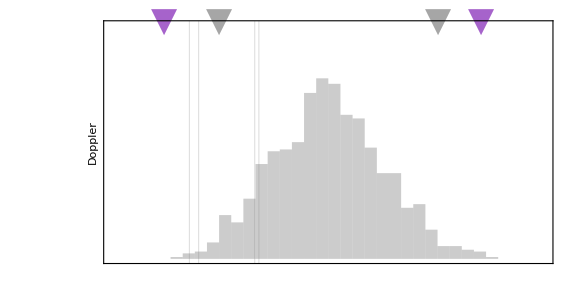

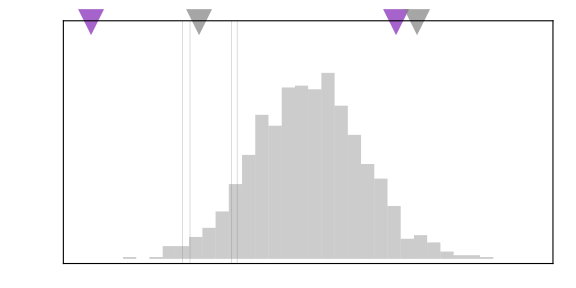

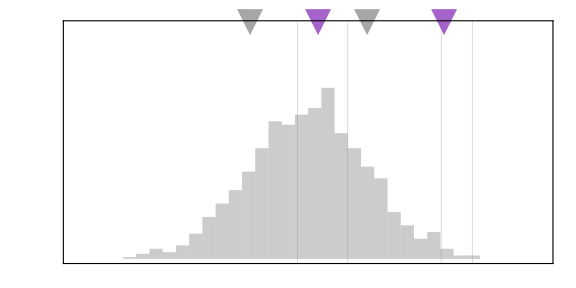

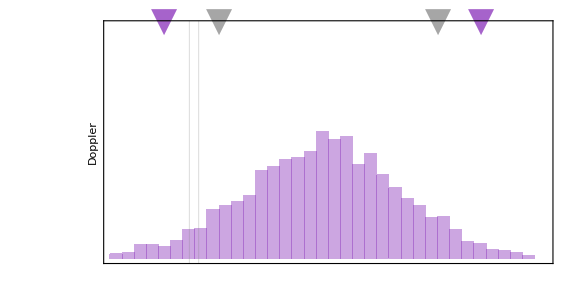

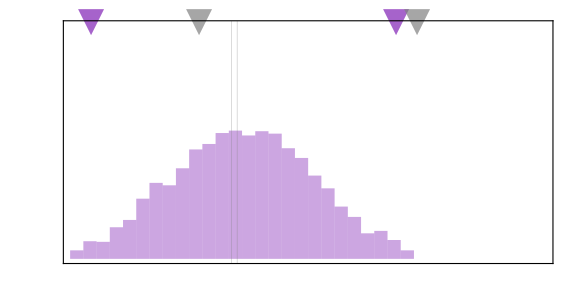

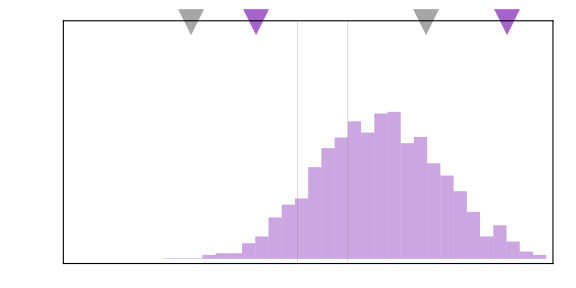

```mathematica
estim=2;
axis=1;
countmax=320*1.2;
doppxNULL=Histogram[Select[vecsistbetaforhistsmicaNULL[[axis]][[estim]],Abs[#]<(plotrange)&],30,ChartStyle->Directive[Opacity[alpha1,color1],EdgeForm[None]],Frame->True,FrameLabel->{Style["",labelfontsize],Style["Doppler",labelfontsize]},GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{(nilcresultswDD[[estim]][[axis]]*c),{color3,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}},{smicaresultswDD[[estim]][[axis]]*c+16,{color4,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finaldoppxNULL=Show[{doppxNULL,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
axis=2;
countmax=320*1.2;
doppyNULL=Histogram[Select[vecsistbetaforhistsmicaNULL[[axis]][[estim]],Abs[#]<(plotrange)&],30,ChartStyle->Directive[Opacity[alpha1,color1],EdgeForm[None]],Frame->True,GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{(nilcresultswDD[[estim]][[axis]]*c),{color3,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}},{smicaresultswDD[[estim]][[axis]]*c,{color4,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},FrameLabel->{Style["",labelfontsize],Style["",labelfontsize]},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finaldoppyNULL=Show[{doppyNULL,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
axis=3;
countmax=290*1.44;
doppzNULL=Histogram[Select[vecsistbetaforhistsmicaNULL[[axis]][[estim]],#<(plotrange)&],30,ChartStyle->Directive[Opacity[alpha1,color1],EdgeForm[None]],Frame->True,GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{(nilcresultswDD[[estim]][[axis]]*c),{color3,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}},{smicaresultswDD[[estim]][[axis]]*c,{color4,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},FrameLabel->{Style["",labelfontsize],Style["",labelfontsize]},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finaldoppzNULL=Show[{doppzNULL,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
countmax=320*1.2;
axis=1;
doppx=Histogram[dipole[[axis]]+Select[vecsistbetaforhistsmica[[axis]][[estim]],Abs[#]<(plotrange-20)&],40,ChartStyle->Directive[Opacity[alpha2,color2],EdgeForm[None]],Frame->True,FrameLabel->{Style["",labelfontsize],Style["Doppler",labelfontsize]},GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finaldoppx=Show[{doppx,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
axis=2;
countmax=320*1.2;
doppy=Histogram[dipole[[axis]]+Select[vecsistbetaforhistsmica[[axis]][[estim]],Abs[#]<(plotrange-260)&],20,ChartStyle->Directive[Opacity[alpha2,color2],EdgeForm[None]],Frame->True,GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},FrameLabel->{Style["",labelfontsize],Style["",labelfontsize]},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finaldoppy=Show[{doppy,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
axis=3;
countmax=290*1.44;
doppz=Histogram[dipole[[axis]]+Select[vecsistbetaforhistsmica[[axis]][[estim]],#<(plotrange-dipole[[axis]]-5)&],30,ChartStyle->Directive[Opacity[alpha2,color2],EdgeForm[None]],Frame->True,GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},FrameLabel->{Style["",labelfontsize],Style["",labelfontsize]},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistsmicaNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistsmica[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finaldoppz=Show[{doppz,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
```

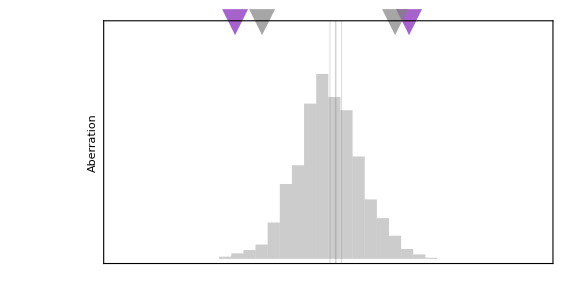

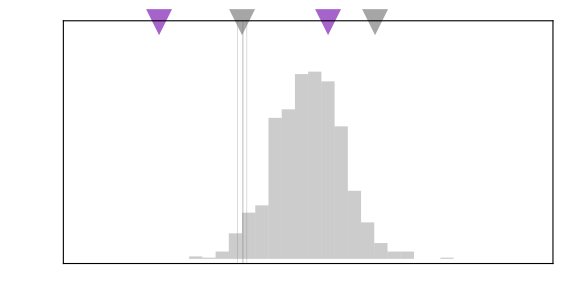

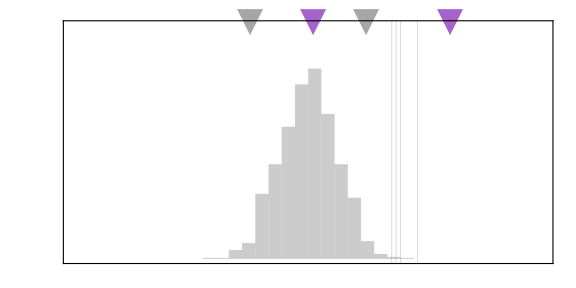

1

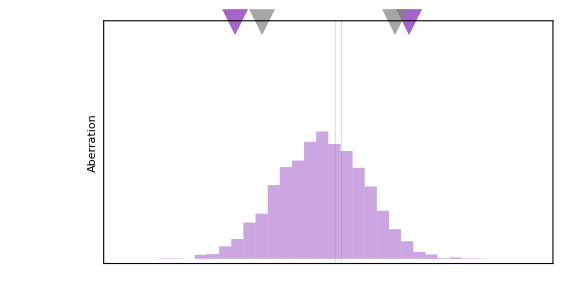

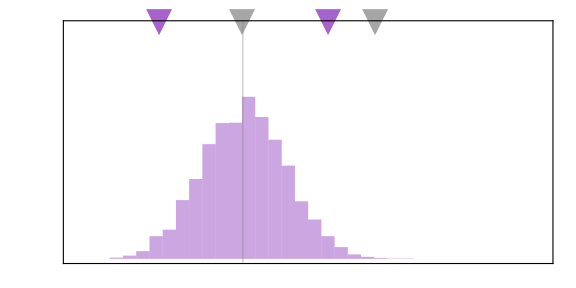

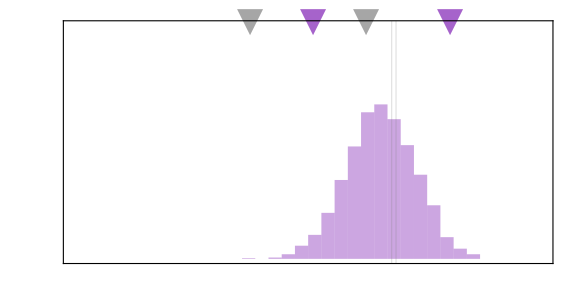

```mathematica
estim=1;
axis=1;
countmax=530*1.2;
abxNULL=Histogram[vecsistbetaforhistsmicaNULL[[axis]][[estim]],20,ChartStyle->Directive[Opacity[alpha1,color1],EdgeForm[None]],Frame->True,FrameLabel->{Style["",labelfontsize],Style["Aberration",labelfontsize]},GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}},{smicaresultswDD[[estim]][[axis]]*c,{color4,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}},{(nilcresultswDD[[estim]][[axis]]*c),{color3,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},FrameLabel->{Style["",21,Bold],""},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistnilcNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistnilcNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistnilc[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistnilc[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finalabxNULL=Show[{abxNULL,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
axis=2;
countmax=480*1.2;
abyNULL=Histogram[vecsistbetaforhistsmicaNULL[[axis]][[estim]],20,ChartStyle->Directive[Opacity[alpha1,color1],EdgeForm[None]],Frame->True,GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}},{smicaresultswDD[[estim]][[axis]]*c+14,{color4,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}},{(nilcresultswDD[[estim]][[axis]]*c),{color3,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},FrameLabel->{Style["",labelfontsize],Style["",labelfontsize]},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistnilcNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistnilcNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistnilc[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistnilc[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finalabyNULL=Show[{abyNULL,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
axis=3;
countmax=530*1.34;
abzNULL=Histogram[vecsistbetaforhistsmicaNULL[[axis]][[estim]],20,ChartStyle->Directive[Opacity[alpha1,color1],EdgeForm[None]],Frame->True,GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{(nilcresultswDD[[estim]][[axis]]*c),{color3,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}},{smicaresultswDD[[estim]][[axis]]*c,{color4,Thickness[0.014],Opacity[1],Dashing[{r1,r2}]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},FrameLabel->{Style["",labelfontsize],Style["",labelfontsize]},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistnilcNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistnilcNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistnilc[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistnilc[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finalabzNULL=Show[{abzNULL,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
countmax=530*1.2;
axis=1
abx=Histogram[dipole[[axis]]+vecsistbetaforhistsmica[[axis]][[estim]],20,(*ChartLegends->Placed[SwatchLegend[{color2,color1},{legend1,legend2},LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&),LabelStyle->{FontSize->9},LegendMarkerSize->23,LegendMargins->0.5,Alignment->{Left,Center}],{0.22,0.68}],*)ChartStyle->Directive[Opacity[alpha2,color2],EdgeForm[None]],Frame->True,FrameLabel->{Style["",labelfontsize],Style["Aberration",labelfontsize]},GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},FrameLabel->{Style["",21,Bold],""},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistnilcNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistnilcNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistnilc[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistnilc[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finalabx=Show[{abx,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
axis=2;
countmax=480*1.2;
aby=Histogram[dipole[[axis]]+vecsistbetaforhistsmica[[axis]][[estim]],30,ChartStyle->Directive[Opacity[alpha2,color2],EdgeForm[None]],Frame->True,GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},FrameLabel->{Style["",labelfontsize],Style["",labelfontsize]},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistnilcNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistnilcNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistnilc[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistnilc[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finalaby=Show[{aby,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
axis=3;
countmax=530*1.34;
abz=Histogram[dipole[[axis]]+vecsistbetaforhistsmica[[axis]][[estim]],20,ChartStyle->Directive[Opacity[alpha2,color2],EdgeForm[None]],Frame->True,GridLines->{{{(nilcresults[[estim]][[axis]]*c),{Blue,Thickness[0.014],Opacity[1]}},{smicaresults[[estim]][[axis]]*c,{Red,Thickness[0.014],Opacity[1]}}},{}},Method->{"GridLinesInFront"->True},PlotRange->{{-plotrange,plotrange},{0,countmax}},FrameStyle->AbsoluteThickness[frametickness],FrameTicks-> {{None,None},{ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800],ticks2[-1000,1000,50,200,400,0.01,True,False,-800,800]}},FrameTicksStyle->{{{FontOpacity->0,FontSize->0},{}},{{FontSize->ticksfontsize,Thickness[.0025]},{FontSize->10,FontOpacity-> 0,Thickness[.0025]}}},FrameLabel->{Style["",labelfontsize],Style["",labelfontsize]},AspectRatio->1/2,ImageSize->Large,ChartLayout-> "Overlapped"];
insetcharP1null=Graphics[Text[Style["▼",color1t,trianglesize],{2*StandardDeviation[vecsistbetaforhistnilcNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1null=Graphics[Text[Style["▼",color1t,trianglesize],{-2*StandardDeviation[vecsistbetaforhistnilcNULL[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharP1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]+2*StandardDeviation[vecsistbetaforhistnilc[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
insetcharM1=Graphics[Text[Style["▼",color2t,trianglesize],{dipole[[axis]]-2*StandardDeviation[vecsistbetaforhistnilc[[axis]][[estim]]],triangleposcorrection*countmax},{0,0}]];
finalabz=Show[{abz,insetcharP1,insetcharM1,insetcharP1null,insetcharM1null}]
```

```mathematica
Export["abx_hist.pdf",finalabx];Export["aby_hist.pdf",finalaby];Export["abz_hist.pdf",finalabz];
Export["doppx_hist.pdf",finaldoppx];Export["doppy_hist.pdf",finaldoppy];Export["doppz_hist.pdf",finaldoppz];
Export["pvx_hist.pdf",finalpvx];Export["pvy_hist.pdf",finalpvy];Export["pvz_hist.pdf",finalpvz];
```

```mathematica
(*histresult=GraphicsGrid[{{finalabx,finalaby,finalabz},{finaldoppx,finaldoppy,finaldoppz},{finalpvx,finalpvy,finalpvz}},Background->White,ImageSize->1200,Spacings->{-178,-86.4}]*)
```

```mathematica
Export["doppz_hist-mq.pdf",finaldoppz]
```

doppz_hist-mq.pdf

```mathematica
alpha1
```

0.4

```mathematica
adjustx[gr_,colorline_,colorx_,opacity_]:=Show[gr,Graphics[{EdgeForm[{Thickness[.007],Blend[{Black,colorline},.8]}],FaceForm[{Blend[{White,colorx},.3],Opacity[opacity]}],Polygon[Cases[gr,Rectangle[{x1_,y1_},{x2_,y2_},_]:>Sequence[{x1,y1},{x1,y2},{x2,y2},{x2,y1}],Infinity]//.{s___,a_,a_,e___}:>{s,e}]}]];
```

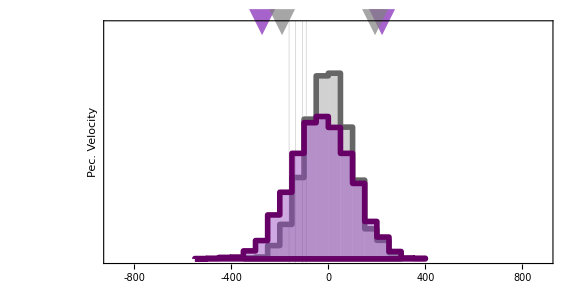

histgoodpvxfinal.pdf

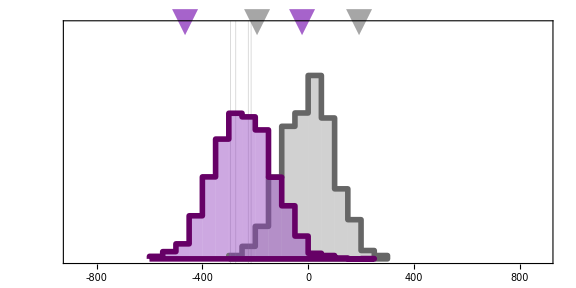

histgoodpvyfinal.pdf

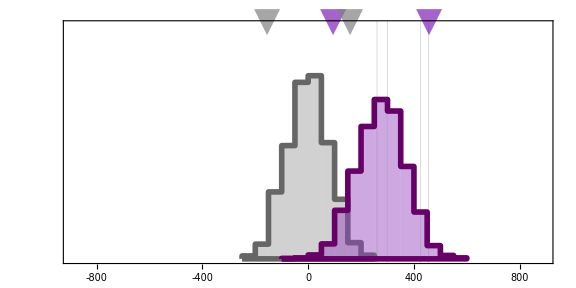

histgoodpvzfinal.pdf

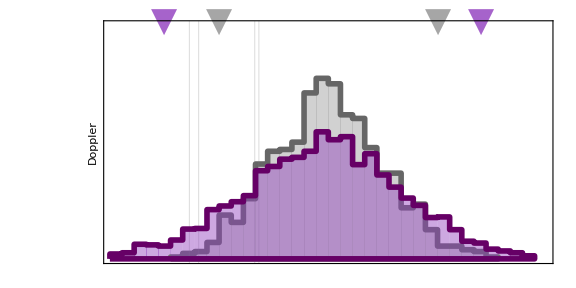

histgooddoppxfinal.pdf

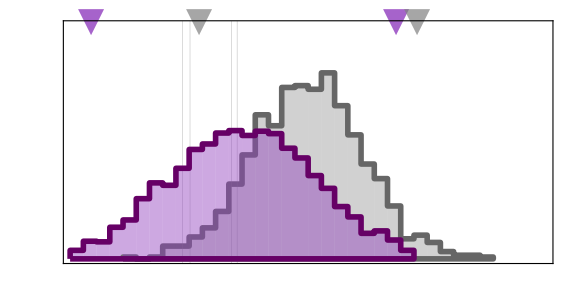

histgooddoppyfinal.pdf

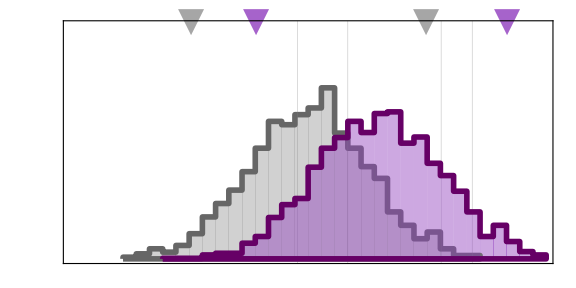

histgooddoppzfinal.pdf

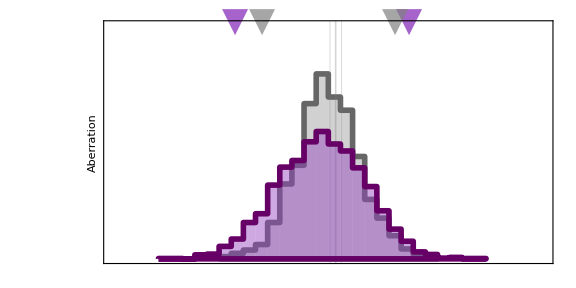

histgoodabxfinal.pdf

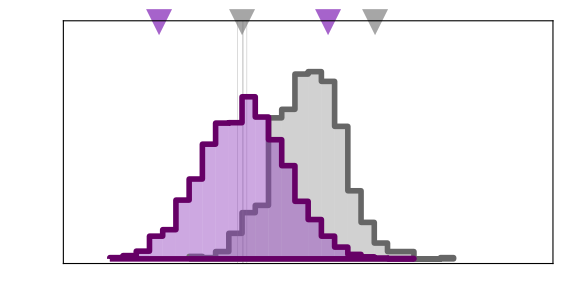

histgoodabyfinal.pdf

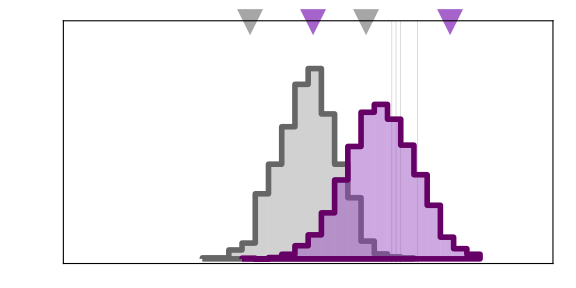

histgoodabzfinal.pdf

```mathematica
(* tem que fazer isso pra cada hist. (um pro dipolo, um pro nulo) e depois juntar *)
histgoodpvxNULL=adjustx[pvxNULL,Gray,color1,alpha1];
histgoodpvx=adjustx[finalpvx,Purple,color2,0.1];
histgoodpvxfinal=Show[{histgoodpvxNULL,histgoodpvx}]
Export["histgoodpvxfinal.pdf",histgoodpvxfinal]
histgoodpvyNULL=adjustx[pvyNULL,Gray,color1,alpha1];
histgoodpvy=adjustx[finalpvy,Purple,color2,0.1];
histgoodpvyfinal=Show[{histgoodpvyNULL,histgoodpvy}]
Export["histgoodpvyfinal.pdf",histgoodpvyfinal]
histgoodpvzNULL=adjustx[pvzNULL,Gray,color1,alpha1];
histgoodpvz=adjustx[finalpvz,Purple,color2,0.1];
histgoodpvzfinal=Show[{histgoodpvzNULL,histgoodpvz}]
Export["histgoodpvzfinal.pdf",histgoodpvzfinal]
histgooddoppxNULL=adjustx[doppxNULL,Gray,color1,alpha1];
histgooddoppx=adjustx[finaldoppx,Purple,color2,0.1];
histgooddoppxfinal=Show[{histgooddoppxNULL,histgooddoppx}]
Export["histgooddoppxfinal.pdf",histgooddoppxfinal]
histgooddoppyNULL=adjustx[doppyNULL,Gray,color1,alpha1];
histgooddoppy=adjustx[finaldoppy,Purple,color2,0.1];
histgooddoppyfinal=Show[{histgooddoppyNULL,histgooddoppy}]
Export["histgooddoppyfinal.pdf",histgooddoppyfinal]
histgooddoppzNULL=adjustx[doppzNULL,Gray,color1,alpha1];
histgooddoppz=adjustx[finaldoppz,Purple,color2,0.1];
histgooddoppzfinal=Show[{histgooddoppzNULL,histgooddoppz}]
Export["histgooddoppzfinal.pdf",histgooddoppzfinal]
histgoodabxNULL=adjustx[abxNULL,Gray,color1,alpha1];
histgoodabx=adjustx[finalabx,Purple,color2,0.1];
histgoodabxfinal=Show[{histgoodabxNULL,histgoodabx}]
Export["histgoodabxfinal.pdf",histgoodabxfinal]
histgoodabyNULL=adjustx[abyNULL,Gray,color1,alpha1];
histgoodaby=adjustx[finalaby,Purple,color2,0.1];
histgoodabyfinal=Show[{histgoodabyNULL,histgoodaby}]
Export["histgoodabyfinal.pdf",histgoodabyfinal]
histgoodabzNULL=adjustx[abzNULL,Gray,color1,alpha1];
histgoodabz=adjustx[finalabz,Purple,color2,0.1];
histgoodabzfinal=Show[{histgoodabzNULL,histgoodabz}]
Export["histgoodabzfinal.pdf",histgoodabzfinal]
(*Export["good.pdf",histgoodpvxfinal]*)
```

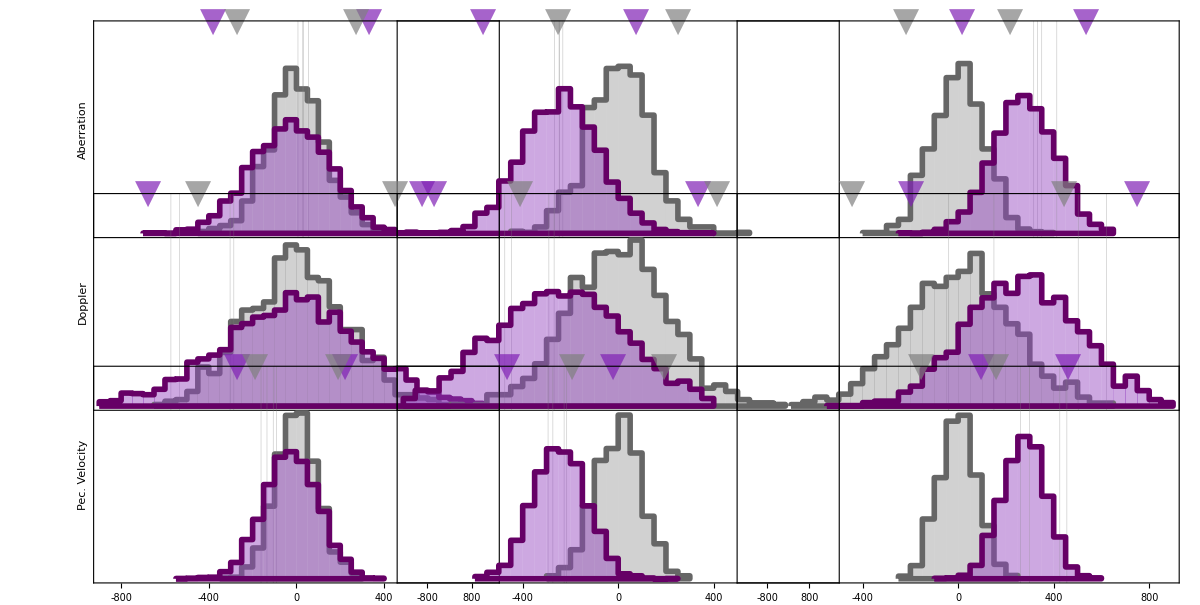

```mathematica
histresult=GraphicsGrid[{{histgoodabxfinal,histgoodabyfinal,histgoodabzfinal},{histgooddoppxfinal,histgooddoppyfinal,histgooddoppzfinal},{histgoodpvxfinal,histgoodpvyfinal,histgoodpvzfinal}},Background->White,ImageSize->1200,Spacings->{-199.5,-96.5}]
```

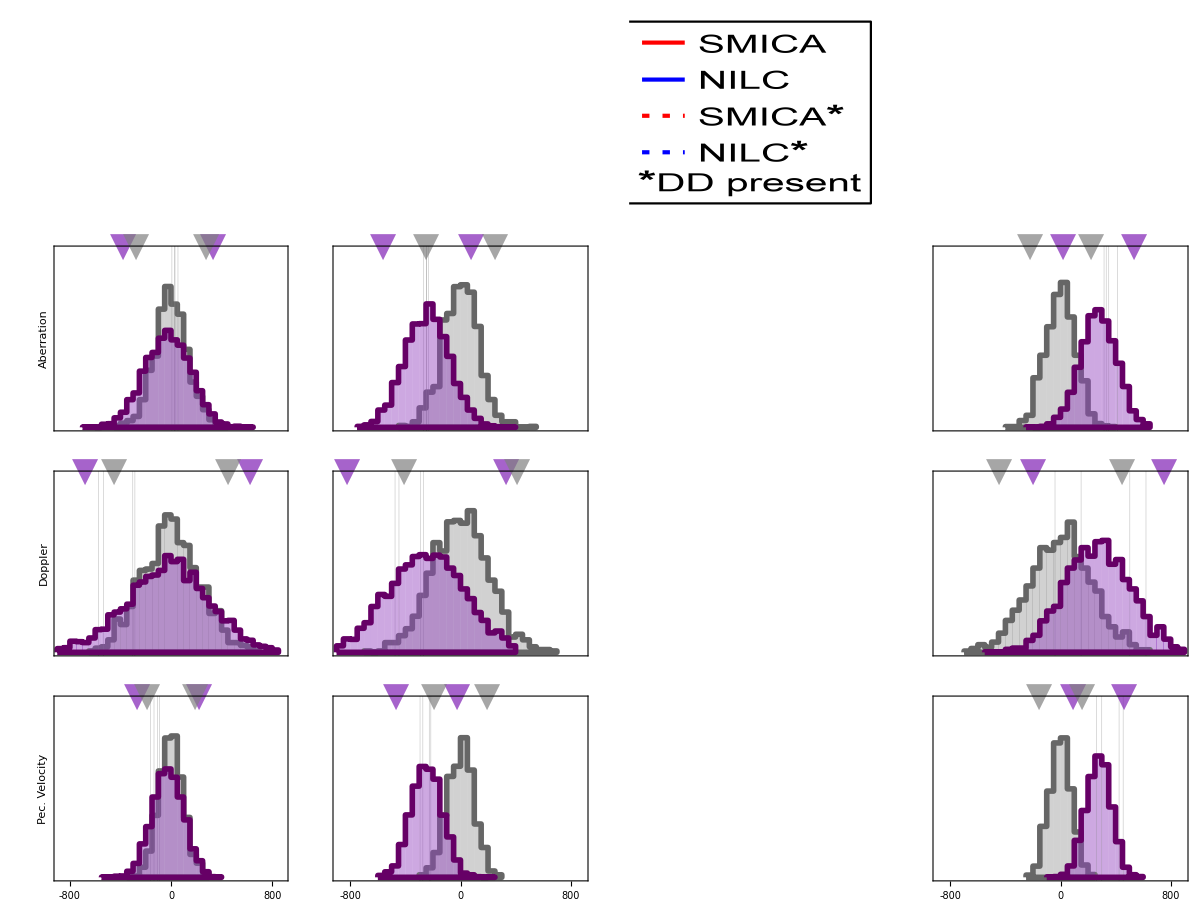

```mathematica
sublegend1=Graphics[Text[Import["legend1_v2.pdf"][[1]],{90,-22}]];
sublegend2=Graphics[Text[Import["legend2_v3.pdf"][[1]],{846,-57.3}]];
histresultfinal=Show[histresult,sublegend1,sublegend2]
```

```mathematica
Export["histresultfinal2.pdf",histresultfinal]
```

histresultfinal2.pdf

```mathematica
(*a=ListPlot[{{1,2,3,4},{0.4,3,2,5},{1,2,3,4},{0.4,3,2,5}},PlotStyle->{{Red,AbsoluteThickness[3]},{Blue,AbsoluteThickness[3]},{Red,Dashing[{0.017,0.03}],AbsoluteThickness[3]},{Blue,Dashing[{0.017,0.03}],AbsoluteThickness[3]}},PlotLegends->LineLegend[{"SMICA","NILC","SMICA^*","NILC^*"},LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&),LabelStyle->{FontSize->9},LegendMarkerSize->23,LegendMargins->0.5,Alignment->{Left,Center}],Joined->True]*)
```